## Spherical Harmonics

```mathematica
shAssumptions={Element[θ,Reals],Element[ϕ,Reals],θ≥0,ϕ≥0,θ≤Pi,ϕ≤2Pi};

(* Normalization function *)
shK[m_Integer, l_Integer]:=√(((2 l+1) (l-Abs[m])!)/(4 π (l + Abs[m])!))

(* Associated Legendre polynomial *)
shP[m_Integer, l_Integer, x_] :=Which[ 
m== l, (-1)^m(2m-1)!!(1-x^2)^(m/2), 
m== (l-1), x(2m+1)shP[m, m,x],
 True, 1/(l-m)(x(2l-1)shP[m, l-1, x] - (l+m -1)shP[m, l-2, x])]

(* Spherical Harmonic *)
shY[m_Integer, l_Integer] := Simplify[Which[
m > 0, √2 shK[m, l]Cos[m ϕ]shP[m, l, Cos[θ]],
m < 0, √2 shK[m, l]Sin[-m ϕ]shP[-m, l, Cos[θ]],
m == 0, shK[0, l]shP[0, l, Cos[θ]]], shAssumptions]

(* It is convenient to index the the spherical harmonic functions from 0 to i,the functions below compute the band (l) and in-band index (m) from a function index i *)
shL[i_] := Floor[Sqrt[i]]
shM[i_] := i - shL[i]^2 - shL[i]

(* Rules and assumptions used when converting from spherical coordinates to Cartesian *)
shToCartesianRules={θ->ArcCos[z], ϕ->ArcTan[y/x], z^2->1-x^2-y^2};
shToCartesianAssumptions = {x^2+y^2+z^2==1, x>0, y>0, z>0};

(* Convert a spherical harmonic function in spherical coordinates to Cartesian FixedPoint repeatedly applies the transformation functions and simplifies until we obtain the standard form, the rules try to minimise the power of z in the result *)
shToCartesian[f_] := FixedPoint[Simplify[#/.shToCartesianRules, shToCartesianAssumptions]&, TrigExpand[f]]
```

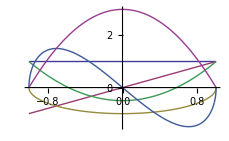

```mathematica
(* The first 6 Legendre polynomials *)
Plot[{shP[0, 0, x],
	shP[0, 1, x],
	shP[1, 1, x],
	shP[0, 2, x],
	shP[1, 2, x],
	shP[2, 2, x]}, {x, -1, 1}, AxesStyle->6]
```

```mathematica
(* First 3 bands in Cartesian coordinates *)
Column[Table[shToCartesian[shY[m, l]], {l, 0, 2}, {m, -l, l} ], Center]
```

{1/(2 √π)}
{-1/2 √(3/π) y,1/2 √(3/π) z,-1/2 √(3/π) x}
{1/2 √(15/π) x y,-1/2 √(15/π) y z,1/4 √(5/π) (-1+3 z^2),-1/2 √(15/π) x z,1/4 √(15/π) (x^2-y^2)}

```mathematica
(* Spherical plot an SH function *)
shPlot[m_, l_] := SphericalPlot3D[Re[Abs[shY[m, l]]], {θ, 0 ,Pi}, {ϕ, 0, 2Pi},{ImageSize->{70, 70},  AxesStyle->4, PlotRange->0.6}]
	
(* Plot first 3 SH bands *)
Column[Table[shPlot[m, l], {l, 0, 2}, {m, -l, l}], Center]
```

{-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Integrate a SH function with respect to itself, expect 1 *)
Integrate[shY[2, 2]shY[2, 2]Sin[θ], {θ, 0, Pi}, {ϕ, 0, 2Pi}]
```

1

```mathematica
(* Integrate a SH function with respect to another in the same band, expect 0 *)
Integrate[shY[-2, 2]shY[2, 2]Sin[θ], {θ, 0, Pi}, {ϕ, 0, 2Pi}]
```

0

## Projection

```mathematica
(* Return a flat array of functions for the bands [0, l] *)
shFunctions[l_] := Table[shY[shM[i], shL[i]], {i, 0, (l+1)^2-1} ]

(* Project spherical function f into basis functions using numerical integration *)
shProject[f_, funcs_] :=Map[NIntegrate[f*#*Sin[θ], {θ, 0, Pi}, {ϕ, 0, 2Pi}, AccuracyGoal->5]&, funcs]

(* Reconstruct a function from the weighted spherical harmonics *)
shExpand[coeffs_, funcs_] := Plus@@ (coeffs*funcs)
```

```mathematica
(* Two light source test function from Robin Green's Gritty Details *)
lightTest := Max[0, 5Cos[θ]-4 ] + Max[0, -4Sin[θ-Pi]*Cos[ϕ-2.5]-3]

(* Calculate the 3rd order function coefficients *)
lightTestCoefficients = N[shProject[lightTest, shFunctions[3]]]

(* Plot original and reconstructed function *)
{SphericalPlot3D[lightTest, {θ, 0 ,Pi}, {ϕ, 0, 2Pi}, PlotRange->1.0],
SphericalPlot3D[shExpand[lightTestCoefficients, shFunctions[3]], {θ, 0 ,Pi}, {ϕ, 0, 2Pi}, PlotRange->1.0]}
```

{0.398802,-0.210524,0.286531,0.281817,-0.314993,4.82714×10^-17,0.131378,-2.77391×10^-17,0.0931792,-0.249606,4.98985×10^-17,0.123359,0.303878,-0.165134,-1.74193×10^-17,-0.0922411}

{-Graphics3D-,-Graphics3D-}

## Ringing

```mathematica
(* Apply ringing reduction to a set of coefficients (Sloan,P.-P.2008. Stupid spherical harmonics tricks) *)
shReduceRinging[a_, k_] := Flatten[MapIndexed[#1/ (1.0 + k*(shL[#2-1])^2(shL[#2-1]+1)^2)&, a]]
```

{0.886227,5.53851×10^-17,1.02333,6.12386×10^-17,-3.84326×10^-18,7.23483×10^-17,0.495416,1.14386×10^-16,-4.35164×10^-17}

{0.886227,5.32549×10^-17,0.983968,5.88832×10^-17,-2.82593×10^-18,5.31973×10^-17,0.364276,8.41071×10^-17,-3.19973×10^-17}

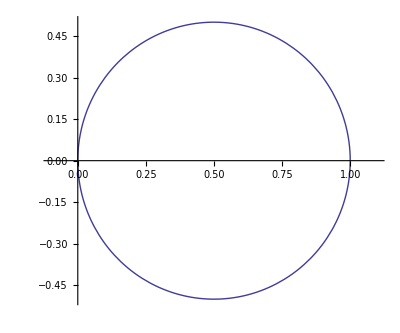
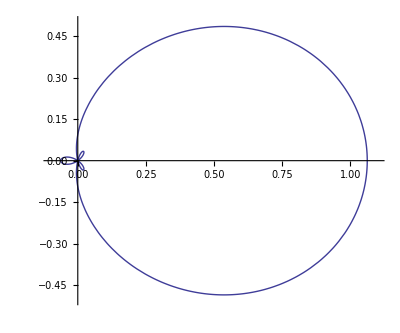
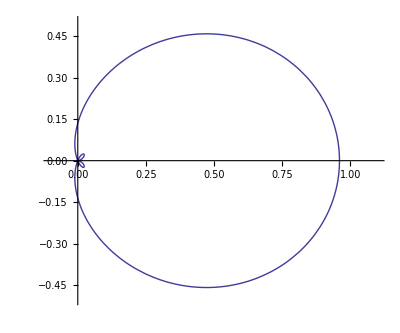

```mathematica
(* Test ringing reduction on Lambertian cosine lobe *)
shLambert := Max[0, Cos[θ]]

(* Project cosine lobe to 3rd order basis *)
shLambertCoefficients = N[shProject[shLambert, shFunctions[2]]]
shLambertCoefficientsWindowed = N[shReduceRinging[shLambertCoefficients, 0.01]]

shLambertFuncs := { 
shLambert,
shExpand[shLambertCoefficients, shFunctions[2]]/.ϕ->0,
shExpand[shLambertCoefficientsWindowed, shFunctions[2]]/.ϕ->0 }

(* Compare cosine lobe, 3rd order projection, 3rd order windowed projection *)
Map[PolarPlot[#,{θ, 0, 2Pi}, ImageSize->Tiny, AxesStyle->4, PlotRange->{{-0.1, 1.1},{-0.5, 0.5}}] &, shLambertFuncs]
```

{0.0844026,3.42717×10^-18,0.139545,3.37098×10^-6,9.0361×10^-19,1.64928×10^-17,0.164113,5.82447×10^-6,9.49481×10^-6}

{0.0844026,3.29536×10^-18,0.134177,3.24133×10^-6,6.64419×10^-19,1.21271×10^-17,0.120671,4.2827×10^-6,6.98148×10^-6}

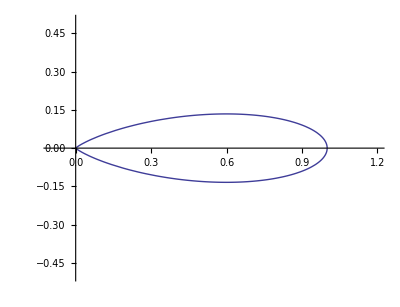
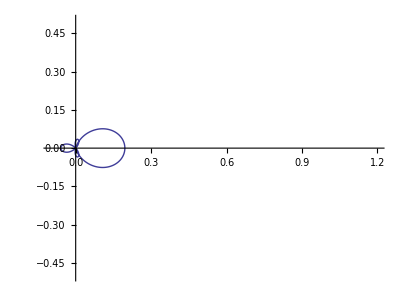
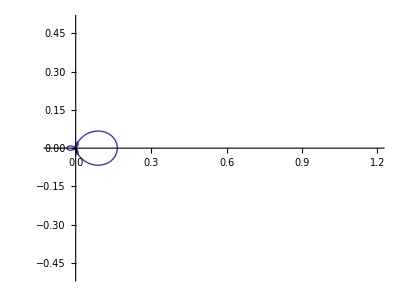

```mathematica
(* Test ringing reduction on a low exponent Phong lobe *)
shPhong := Max[0, Cos[θ]]^20.0

(* Project cosine lobe to 3rd order basis *)
shPhongCoefficients = N[shProject[shPhong, shFunctions[2]]]
shPhongCoefficientsWindowed = N[shReduceRinging[shPhongCoefficients, 0.01]]

(* Compare cosine lobe, 3rd order projection, 3rd order windowed projection *)
shPhongFuncs := {
shPhong,
shExpand[shPhongCoefficients, shFunctions[2]]/.ϕ->0,
shExpand[shPhongCoefficientsWindowed, shFunctions[2]]/.ϕ->0}

Map[PolarPlot[#,{θ,0,2Pi},ImageSize->Tiny, AxesStyle->4, PlotRange->{{-0.1, 1.2},{-0.5, 0.5}}] &,shPhongFuncs]
```